## 1. Wolfram其人，MMA与Form语言

### 1.1 Stephen Wolfram

-Graphics- | 15岁在Nuclear Physics B、Physical Review D 等期刊上发表量子场论与粒子物理相关文章、20岁在CIT获得粒子物理PhD、与费曼一起进行原胞自动机的研究、
为推进自动化科学计算创建Wolfram Research公司、试图用“自然的科学结构自动涌现”的视角寻找新科学

### 1.2 Mathematica

使用Wolfram脚本语言的科学计算软件+内置功能强大的函数集

优点：1. 使用极其方便，人类友好
 	     2. 自由度大，几乎所有的指令都可以重载，从科学计算到图片处理都可以使用
 	     3. 使用者广，有各种科学计算扩展库可以使用
缺点：运行速度较慢，特别是对大规模计算

使用文件后缀：.nb/.m/.wl
.nb：notebook，Mathematica自带的前端文本编辑器
.m/.wl 纯文本文件，Mathematica内核可识别读取的代码
在终端中使用Mathematica：
wolfram -noprompt -script “$HOME/qpdf/qpdfqqthreeloops/ffrunBC/familymap2.wl”

### 1.3 Form

https://github.com/vermaseren/form
更像C语言的符号计算语言，编译器轻巧，运行速度快

## 2. 帮助文档

99%的编程知识都是自学来的！！！
Mathematica所有的内置命令都有对应的帮助文档讲解，从输入输出格式到基本应用应有尽有，甚至炫技应用都有收录
中文帮助文档基本不存在翻译问题，所以如果不是对自己英语特别自信一定要选择中文版的MMA

## 3. 表达式

### 3.1 表达式定义

```mathematica
(*表达式是MMA中的基本“数据类型”,所有的表达式都是函数*)
```

```mathematica
a=3
b3=7.8
$D="I love mathematica"
μ3=3^100
c=a
f[a,b3,$D,c,r]
```

3

7.8

I love mathematica

515377520732011331036461129765621272702107522001

3

f[3,7.8,I love mathematica,3,r]

```mathematica
Clear[a,$D,μ3];
a
$D
μ3
```

a

$D

μ3

```mathematica
(*字符串与表达式不一样，某种意义上可以看做“常表达式”*)
```

```mathematica
"t"=5
"t"
```

Set::setraw: Cannot assign to raw object t.

5

t

```mathematica
ToExpression["a"]==a
```

True

### 3.2 括号与常用运算符号

```mathematica
() : 用来确定用算的先后顺序
[] : 用来标志函数的变量
[[]] : 用于指定表达式特定位置
{} : 表示一个列表
```

```mathematica
list={1,{here},-Graphics-,"yes!yes!",F[91]}
list[[3]]
```

{1,{here},-Graphics-,yes!yes!,F[91]}

-Graphics-

```mathematica
list[[3;;5]]
Take[list,{3,5}]
list[[2]][[1]]
list[[2,1]]
```

{-Graphics-,yes!yes!,F[91]}

{-Graphics-,yes!yes!,F[91]}

here

here

```mathematica
Information[here]
```

```mathematica
基本代数运算：+ - * / ^
```

```mathematica
7*7
7 7
```

```mathematica
%:上次输出
%n==Out[n]:第n次输出
```

```mathematica
%
%5
```

I love mathematica

```mathematica
_==Blank[] :缺省符号，可代表任意 Wolfram 语言表达式，通常模式匹配和定义函数时候使用
_h==Blank[h]:表示任意类型为h的表达式
```

```mathematica
?f==Definition[f]: 给出f的定义
?? f==Information[f]: 给出f的所有信息
```

```mathematica
?True
```

```mathematica
内置常量
```

```mathematica
Pi
N[Pi]
E
N[E]
N[EulerGamma]
```

π

3.14159

ⅇ

2.71828

0.577216

### 3.3 头部与结构

```mathematica
f[[0]]==Head[f]:表达式的头部，表示这一表达式最外层属于什么类型
```

```mathematica
(*为什么说所有的表达式都是函数*)
```

```mathematica
Head[{}]
(a+b)[[0]]
3[[0]]
Head[Cos[x]]
Head[-Graphics-]
```

```mathematica
a+b[[0]]
```

```mathematica
Length:表达式的最外层元素个数
```

```mathematica
Length[{{1,2,3},{4,5}}]
```

```mathematica
LeafCount:给出不可再约化的子表达式个数
```

```mathematica
LeafCount[{{1,2,3},{4,5}}]
```

```mathematica
Level[_,n]:给出第n层所有的子表达式
```

```mathematica
Level[{{1,2,3},{4,5}},{0,Infinity}]
Level[x+y^z,{0,Infinity}]
```

```mathematica
Level[{{1,2,3},{4,5}},{-1},Heads->True]
Level[x+y^z,{-1},Heads->True]
```

```mathematica
(*LeafCount[X]=Length[Level[X,{-1},Heads->True]]*)
```

### 3.4 属性

```mathematica
Attributes:查看属性
```

```mathematica
Attributes[Pi]
```

```mathematica
Attributes[Plus]
```

```mathematica
SetAttributes:设置属性
```

```mathematica
f[1,2]==f[2,1]
```

```mathematica
SetAttributes[f,Orderless]
f[1,2]==f[2,1]
```

### 3.5 格式

```mathematica
sigma={{{0,1},{1,0}},{{0,-I},{I,0}},{{1,0},{0,-1}}}
```

```mathematica
StandardForm/@sigma
```

```mathematica
TraditionalForm/@sigma
```

```mathematica
InputForm[x^2]
```

```mathematica
OutputForm[x^2]
```

```mathematica
FullForm/@sigma
```

```mathematica
FullForm[-Graphics-]
```

Image[NumericArray[List[1],"UnsignedInteger8"],"Byte",Rule[ColorSpace,"RGB"],Rule[Interleaving,True]]
 |  |  |  |

## 4. 表达式操作

### 4.1 映射

```mathematica
f[_],f@_,_//f：表达式直接作为函数输入
```

```mathematica
Simplify[x^2-2x+1]
Simplify@(x^2-2x+1)
(x^2-2x+1)//Simplify
```

(-1+x)^2

(-1+x)^2

(-1+x)^2

```mathematica
Apply[f,_],f@@_:用f替换表达式的头部
```

```mathematica
Times@@(x^2-2x+1)
Apply[g,f[x,y,z]]
```

-2 x^3

g[x,y,z]

```mathematica
Map[f,_],f/@_:作用与表达式第一层中的每一项
```

```mathematica
f/@{x,y,z}
f/@(x+y+z)
```

```mathematica
{f[x],f[y],f[z]}
```

{f[x],f[y],f[z]}

```mathematica
Thread:将列表中的项逐项传递到函数中
```

```mathematica
Thread[f[{a,b,c},{d,e,f}]]
Thread[{a,b,c}->{d,e,f}]
```

{f[3,d],f[b,e],f[3,f]}

{3→d,b→e,3→f}

```mathematica
列表的代数运算默认是逐项进行的
```

```mathematica
{a,b,c}+{d,e,f}
{a,b,c} {d,e,f}
```

{3+d,b+e,3+f}

{3 d,b e,3 f}

```mathematica
Thread 也可以用于非列表表达式，但要指定头部
```

```mathematica
Thread[f[a+b+c],Plus]
```

f[6]+f[b]

### 4.2 结构调整

```mathematica
Simplify:将表达式转化为最短字符串的形式
```

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

```mathematica
Together:合并有理表达式并消去分子分母公因子
```

```mathematica
x^2/(x^2-1)+x/(x^2-1)
Together[x^2/(x^2-1)+x/(x^2-1)]
```

```mathematica
Together[E^(I x)/Sin[x]-E^(-I x)/Sin[x]]
```

```mathematica
Apart:把有理表达式分解为部分分式
```

```mathematica
(x^5-2)/((1+x+x^2)(2+x)(1-x))
Apart[(x^5-2)/((1+x+x^2)(2+x)(1-x))]
```

```mathematica
Expand: 展开表达式中的有理部分（整数次乘积）
```

```mathematica
Expand[(x^5-2)((1+x+x^2)(2+x)(1-x))]
```

```mathematica
Factor
```

```mathematica
Factor[-4-2 x+4 x^3+2 x^4+2 x^5+x^6-2 x^8-x^9]
```

```mathematica
Sort/SortBy
```

```mathematica
Sort[{1,3,5,4,2}]
f[x_]:=-x;
SortBy[{1,3,5,4,2},f]
```

```mathematica
Clear[f]
```

```mathematica
添加元素
Append,AppendTo,Prepend,PrependTo
```

```mathematica
Append,Prepend:不改变原来的表达式
AppendTo,PrependTo:改变原来的表达式
```

```mathematica
list={a,b,c}
Append[list,d]
list
AppendTo[list,d]
list
```

```mathematica
(*对Orderless的表达式，谨慎使用*)
```

```mathematica
x=a+b+c
AppendTo[x,a0]
x
```

```mathematica
Clear[x,list]
```

```mathematica
Join:连接两个列表
```

```mathematica
Join[{a,b,c},{1,2,3}]
```

```mathematica
Partition:按照长度划分列表
Partition[{1,2,3,4,5,6,7},3]
```

```mathematica
Split:按照元素划分列表
```

```mathematica
Split[{a,a,b,b,c,c}];
```

```mathematica
Union,Intersection,Complement
```

```mathematica
Flatten:把多层列表变为只有一层的列表
```

```mathematica
Flatten[{{1},{{2},3},4}]
```

```mathematica
Transpose:转置列表的前两层
```

```mathematica
Collect:把特定变量相同次幂的部分组合到一起
```

```mathematica
Collect[a b+a c+a^2 c+Sin[a]s1+Gamma[a]s2+a^2 Sin[b],a]
```

```mathematica
Series:展开为幂级数
```

### 4.3 替换

```mathematica
/.Replace:根据特定规则替换表达式中的内容
```

```mathematica
Log[m^2/(p^2-m^2)]/.{m->1,p->2}
```

```mathematica
Log[m^2/(p^2-m^2)]/.p->k
```

```mathematica
->Rule:描述替换的规则
:>RuleDelayed:延迟替换，先替换再计算被替换的内容，相当于定义了一个局域变量用于替换
```

```mathematica
Log[m^2/(p^2-m^2)]/.Log[x_*y_]:>Log[x]+Log[y]
```

```mathematica
x=1
Log[m^2/(p^2-m^2)]/.Log[x_*y_]->Log[x]+Log[y]
```

```mathematica
Clear[x]
```

### 4.4 筛选

```mathematica
Select:按照一定要求选取表达式中的内容
```

```mathematica
Select[{1,3,-Graphics-,-1,x},Positive]
```

```mathematica
Position:匹配具有特定结构的表达式并给出位置
```

```mathematica
Position[(a+b)(c+b)(a+k),a+_]
```

```mathematica
((a+b)(c+b)(a+k))[[1]]
((a+b)(c+b)(a+k))[[3]]
```

```mathematica
Extract:按照位置提取内容
```

```mathematica
Extract[(a+b)(c+b)(a+k),Position[(a+b)(c+b)(a+k),a+_]]
```

```mathematica
Delete:按照位置删除
```

```mathematica
Delete[(a+b)(c+b)(a+k),Position[(a+b)(c+b)(a+k),a+_]]
```

```mathematica
Cases:匹配具有特定结构的表达式并给出内容
```

```mathematica
Cases[(a+b)(c+b)(a+k),a+_]
```

```mathematica
(*值得注意的是Cases函数只能匹配第一层的结构，例如*)
Cases[(a+b)^2 (c+b)(a+k),a+_]
```

```mathematica
DeleteCases
```

```mathematica
GatherBy:按照特定函数结果将列表中的元素分类
```

```mathematica
GatherBy[{1,3,-Graphics-,-1,x},Head]
```

## 5. 控制语句

### 5.1 循环

```mathematica
For
While
Do
```

```mathematica
Table:生成一个表格
```

```mathematica
Table[{},{i,1,5}]
```

{{},{},{},{},{}}

```mathematica
Nest:将函数重复作用n次
```

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
Fold:将函数重复作用n次，每一次作用都引入新的参数
```

```mathematica
Fold[f,x,{a,b,c}]
```

f[f[f[x,3],b],3]

```mathematica
Tuples:产生列表元素的重复排列
```

```mathematica
Tuples[{a,b,c},3]
```

{{3,3,3},{3,3,b},{3,3,3},{3,b,3},{3,b,b},{3,b,3},{3,3,3},{3,3,b},{3,3,3},{b,3,3},{b,3,b},{b,3,3},{b,b,3},{b,b,b},{b,b,3},{b,3,3},{b,3,b},{b,3,3},{3,3,3},{3,3,b},{3,3,3},{3,b,3},{3,b,b},{3,b,3},{3,3,3},{3,3,b},{3,3,3}}

```mathematica
Tuples 可以用于做外积
```

```mathematica
Tuples[{{a,b,c},{d,e,f}}]
```

{{3,d},{3,e},{3,f},{b,d},{b,e},{b,f},{3,d},{3,e},{3,f}}

```mathematica
Sum
```

Sum

### 5.2 条件

```mathematica
If
Switch
```

```mathematica
(*判断语句*)
```

```mathematica
a=1;
b=1;
a==b
a===b
```

True

True

```mathematica
(*==,!=，比较数值*)
(*=== , =!= , 比较表达式整体*)
```

```mathematica
Clear[a,b];
a==b
a===b
```

a==b

False

```mathematica
FreeQ
```

```mathematica
IntegerQ
```

### 5.3 并行

```mathematica
Parallelize:自动识别并对表达式进行并行计算
```

```mathematica
ParallelTable
ParallelDo
ParallelSum
```

```mathematica
Kernels
```

```mathematica
LaunchKernels
CloseKernels
```

## 6. 函数

### 6.1 推迟定义与参数

```mathematica
推迟定义的重要性
```

```mathematica
f[x_]:=x^2
f[3]
```

```mathematica
Clear[f]
x=2;
f[x_]=x^2;
f[3]
```

4

```mathematica
指定参数类型
```

```mathematica
Clear[f,x]
f[x_Integer]:=x^2
f[0.5]
```

f[0.5]

```mathematica
设定默认值
```

```mathematica
Clear[f]
f[y_,x_:0]:=y^2+x^2
f[3]
```

9

### 6.2 选项

```mathematica
Options:指定函数的选项
```

```mathematica
Clear[f];
Options[f]={print->True};
f[x_,OptionsPattern[]]:=If[OptionValue[print]==True,Print[x]];
```

```mathematica
f[1,print->False];
```

```mathematica
SetOptions:重置选项默认值
```

```mathematica
SetOptions[f,print->False];
f[1];
```

```mathematica
定义函数时候也可以直接使用
```

```mathematica
Clear[f];
f[x_,OptionsPattern[print->True]]:=If[OptionValue[print]==True,Print[x]];
f[1,print->False];
```

### 6.3 条件

```mathematica
/; Condition,当表达式满足条件语句为True才进行计算
```

```mathematica
Clear[f];
f[x_/;PrimeQ[x]]:=Print[ToString[x]<>" is a prime number"];
f[3]
f[4]
```

3 is a prime number

f[4]

```mathematica
条件的位置含义不同，但是起到相同的效果
```

```mathematica
Clear[f];
f[x_]/;PrimeQ[x]:=Print[ToString[x]<>" is a prime number"];
f[3]
```

```mathematica
Clear[f];
f[x_]:=Print[ToString[x]<>" is a prime number"]/;PrimeQ[x];
f[3]
```

3 is a prime number

### 6.4 纯函数

```mathematica
纯函数也叫匿名函数，是一种简便定义函数的方式
```

```mathematica
f:=N[Sin[#]]&
f[Pi/2]
```

1.

```mathematica
纯函数中使用多个变量
```

```mathematica
f:=#1 Sin[#2]&
f[3,1]
```

3 Sin[1]

```mathematica
使用纯函数作为函数的参数
```

```mathematica
SortBy[{1,3,5,4,2},-#&]
```

{5,4,3,2,1}

### 6.5 模块

```mathematica
Block，Module，模块就是封装起来的一段函数，与python类似
```

```mathematica
Clear[f];
f[x_]:=Module[{a,b,c},
Switch[x,
_Integer,
a=x+1;
Return[a],
_Real,
b=IntegerPart[x]+1;
Return[b],
_,
c="error";
Return[c]]]
f[2]
f[2.3]
f[s]
```

3

3

error

```mathematica
3
```

3

```mathematica
a
```

## 7. 外部交互

### 7.1 文件系统操作

```mathematica
Directory[]
SetDirectory["/Users/lx/Desktop/code/AG"]
NotebookDirectory[]
```

```mathematica
CreateDirectory
DeleteDirectory
FileNames 列出当前目录下的文件
DeleteFile
CreateFile
```

```mathematica
$Path 系统目录，Mathematica寻找外部文件的目录
```

```mathematica
$Path
```

### 7.2 文本文件

```mathematica
Get <<
```

```mathematica
test=<<test
```

```mathematica
Put >>
```

```mathematica
test>>test2
test2=<<test2
```

```mathematica
PutAppend[{q},"test2"]
FilePrint["test2"]
```

{q}

### 7.3 程序包

```mathematica
单个文件中的命令集
```

```mathematica
Get["Singular.m"]
```

```mathematica
完善的程序packages
```

```mathematica
<<FeynCalc`
```

### 7.4 外部程序

```mathematica
Run: 直接调用外部程序
```

```mathematica
RunProcess:调用外部程序并返回程序运行的输出
```

```mathematica
RunProcess[$SystemShell,"StandardOutput","echo hello world\nexit\n"]
```

```mathematica
RunThrough:调用外部程序计算表达式并返回Mathematica
```

```mathematica
RunThrough["cat",magia][[0]]
RunThrough["cat","magia"][[0]]
```

```mathematica
(*进阶：编写符合WSTP规范的C,C++代码，实现用Mathematica直接调用C,C++函数*)
```

```mathematica
StartExternalSession:开启一个外部解释器会话，如python,Julia,Ruby等
ExternalEvaluate:使用外部解释器执行命令
ExternalFunction:使用外部解释器的函数
```

```mathematica
(*由于未知的原因这台电脑没能成功配置python接口，想了解的同学请查阅文档*)
```

### 7.5 读取存储其他格式文件或网络文件

```mathematica
gif=Import["cat.gif"]
```

```mathematica
image=-Graphics-;
Export["peach.png",image]
```

peach.png

```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"]
```

It seems that your Mathematica version is unable to connect to the FeynCalc repository on GitHub.
This might be a network connectivity problem or an issue with Mathematica.
Especially some older versions of Mathematica (8, 9 or 10) and known to cause such problems
on recent versions of Linux, MacOS and Windows when accessing SSL-encrypted urls.

Please check the wiki <https://github.com/FeynCalc/feyncalc/wiki/Installation> for possible workarounds.
Notice that it is also possible to download all the necessary files by hand and install FeynCalc
without an existing internet connection. The required steps are described in the wiki.

Installation aborted!

$Aborted

InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True]

## 8. 简单实例

### 8.1 绘制参数曲线

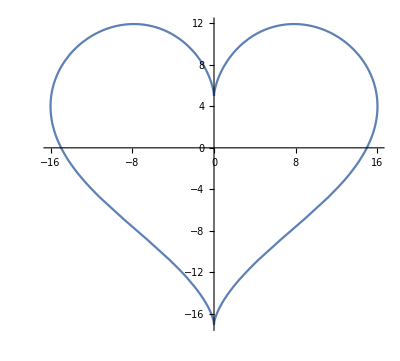

```mathematica
ParametricPlot[{16 Sin[t]^3,13 Cos[t]−5 Cos[2t]−2 Cos[3t]−Cos[4t]},{t,0,2Pi}]
```

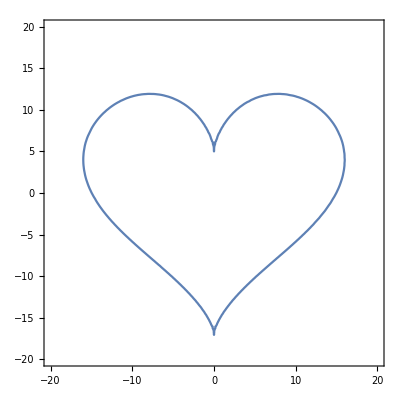

{C:\Users\9999999999999\AppData\Roaming\Mathematica\DocumentationIndices,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Links,C:\Users\9999999999999\AppData\Roaming\Mathematica\Kernel,C:\Users\9999999999999\AppData\Roaming\Mathematica\Autoload,C:\Users\9999999999999\AppData\Roaming\Mathematica\Applications,C:\ProgramData\Mathematica\Kernel,C:\ProgramData\Mathematica\Autoload,C:\ProgramData\Mathematica\Applications,.,C:\Users\9999999999999,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\Packages,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\Autoload,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\Applications,C:\Program Files\Wolfram Research\Mathematica\12.0\AddOns\ExtraPackages,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Kernel\Packages,C:\Program Files\Wolfram Research\Mathematica\12.0\Documentation\English\System,C:\Program Files\Wolfram Research\Mathematica\12.0\SystemFiles\Data\ICC}

```mathematica
gb=GroebnerBasis[{Expand[t^3(x -16((t-1/t)/2I)^3)],Expand[t^4 (13((t+1/t)/2)-5((t^2+1/t^2)/2)-2((t^3+1/t^3)/2)-((t^4+1/t^4)/2)-y)]},{t,x,y}];
ContourPlot[gb[[1]]==0,{x,-20,20},{y,-20,20}]
$Path
```

### 8.3 下载并使用程序包

```mathematica
以xArt为例
```

```mathematica
1.前往 "http://www.xact.es"下载对应操作系统的程序
2.解压至$PATH中路径
3. 运行程序包
$PATH
```

1. http://www.xact.es 前往 下载对应操作系统的程序

2. 解压至$PATH中路径

3. 运行程序包

$PATH

```mathematica
<<xAct`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.5, {2021,2,28}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

### 8.4 使用xArt进行张量计算

```mathematica
(*载入程序包*)
<<xAct`xCoba`;
$DefInfoQ=False;
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
(*定义流形、坐标卡、度规*)
DefManifold[M2,2,{μ,ν,α,β,σ,λ,b,c,d,e,f}];
DefChart[cart,M2,{0,1},{t[],z[]},FormatBasis->{"Partials","Differentials"}];
MatrixMetric=DiagonalMatrix[{-1,1}]/(z[]^2);
met=CTensor[MatrixMetric,{-cart,-cart}];
SetCMetric[met,cart,SignatureOfMetric->{-1,1,0}];
met[-μ,-ν];
e[0]=CTensor[{1,0},{-cart}];
e[1]=CTensor[{0,1},{-cart}];
```

ValidateSymbol::used: Symbol M2 is already used as a manifold.

ValidateSymbol::used: Symbol cart is already used as a mapping.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]

SetCMetric::old: There are already metrics {CTensor[{{-1/z[]^2,0},{0,1/z[]^2}},{-cart,-cart},0],CTensor[{{-1/z[]^2,0},{0,1/z[]^2}},{-cart,-cart},0],CTensor[{{-1/z[]^2,0},{0,1/z[]^2}},{-cart,-cart},0],CTensor[{{-1/z[]^2,0},{0,1/z[]^2}},{-cart,-cart},0],CTensor[{{-1/z[]^2,0},{0,1/z[]^2}},{-cart,-cart},0]} in vbundle 𝕋M2.

```mathematica
(*计算各种张量*)
CD=LC[met];
MetricCompute[met,cart,All];
```

```mathematica
克里斯托弗联络与测地线方程
```

```mathematica
Christoffel[CD][λ,-μ,-ν][[2]]
```

```mathematica
u=CTensor[{t'[],z'[]},{cart}];
a=CTensor[{t''[],z''[]},{cart}];
deqs=Table[(a[λ]+Christoffel[CD][λ,-μ,-ν][[2]]u[μ]u[ν])e[i][-λ]==0,{i,0,1}]
ueq0=met[-μ,-ν]u[μ]u[ν]==0
ueq1=met[-μ,-ν]u[μ]u[ν]==-1
```

{-(2 t'[] z'[])/z[]+t''[]==0,-t'[]^2/z[]-z'[]^2/z[]+z''[]==0}

-t'[]^2/z[]^2+z'[]^2/z[]^2==0

-t'[]^2/z[]^2+z'[]^2/z[]^2==-1

### 8.2 微分方程

```mathematica
Clear[t,z];
eqs=Join[deqs/.{t[]->t[τ],z[]->z[τ],t'[]->t'[τ],z'[]->z'[τ],t''[]->t''[τ],z''[]->z''[τ]},
{ueq0/.{t[]->t[0],z[]->z[0],t'[]->t'[0],z'[]->z'[0],t''[]->t''[0],z''[]->z''[0]}}];
DSolve[eqs,{t[τ],z[τ]},τ]
```

DSolve[{-(2 t'[τ] z'[τ])/z[τ]+t''[τ]==0,-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,-t'[0]^2/z[0]^2+z'[0]^2/z[0]^2==0},{t[τ],z[τ]},τ]

```mathematica
eqs={deqs[[2]],ueq}/.{t[]->t[τ],z[]->z[τ],t'[]->t'[τ],z'[]->z'[τ],t''[]->t''[τ],z''[]->z''[τ]}
rds=DSolve[eqs,{t[τ],z[τ]},τ]
```

{-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,ueq}

DSolve::deqn: Equation or list of equations expected instead of ueq in the first argument {-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,ueq}.

DSolve[{-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,ueq},{t[τ],z[τ]},τ]

```mathematica
nds=NDSolve[Join[eqs,{z[0]==1,z'[0]==1,t[0]==0}],{t[τ],z[τ]},{τ,0,1}]
```

NDSolve::deqn: Equation or list of equations expected instead of ueq in the first argument {-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,ueq,z[0]==1,z'[0]==1,t[0]==0}.

NDSolve[{-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,ueq,z[0]==1,z'[0]==1,t[0]==0},{t[τ],z[τ]},{τ,0,1}]

```mathematica
Plot[t[τ]/.nds[[1]],{τ,0,1}]
```

NDSolve::dsvar: 0.0000204286 cannot be used as a variable.

ReplaceAll::reps: {-t'[0.0000204286]^2/z[0.0000204286]-z'[0.0000204286]^2/z[0.0000204286]+z''[0.0000204286]==0,ueq,z[0]==1,z'[0]==1,t[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-(1. t'[0.0000204286]^2)/z[0.0000204286]-(1. z'[0.0000204286]^2)/z[0.0000204286]+z''[0.0000204286]==0.,ueq,z[0.]==1.,z'[0.]==1.,t[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0204286 cannot be used as a variable.

ReplaceAll::reps: {-t'[0.0204286]^2/z[0.0204286]-z'[0.0204286]^2/z[0.0204286]+z''[0.0204286]==0,ueq,z[0]==1,z'[0]==1,t[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0408368 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
AsymptoticDSolveValue[eqs,{t[τ],z[τ]},τ->0]
```

AsymptoticDSolveValue[{-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,ueq},{t[τ],z[τ]},τ→0]

```mathematica
ads=AsymptoticDSolveValue[Join[eqs,{z[0]==1,z'[0]==1,t[0]==0}],{t[τ],z[τ]},{τ,0,3}]
```

AsymptoticDSolveValue[{-t'[τ]^2/z[τ]-z'[τ]^2/z[τ]+z''[τ]==0,ueq,z[0]==1,z'[0]==1,t[0]==0},{t[τ],z[τ]},{τ,0,3}]

### 8.5 使用FeynArts/FeynCalc计算费曼图

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
LoadModel["QED"];
M$ClassesDescription
M$CouplingMatrices
```

```mathematica
process = {F[1,{1}],V[1]} ->{F[1,{1}],V[1]};
SetOptions[CreateTopologies,ExcludeTopologies->{Tadpoles,WFCorrections,WFCorrectionCTs}];SetOptions[InsertFields,Model -> "QED",InsertionLevel->{Particles}];SetOptions[CreateFeynAmp,PreFactor->1,AmplitudeLevel->{Particles},GaugeRules->{_GaugeXi->GaugeXi}];SetOptions[Paint,PaintLevel->{Particles},FieldNumbers->True,AutoEdit->True];
```

SetOptions::optnf: ExcludeTopologies is not a known option for CreateTopologies.

SetOptions::optnf: Model is not a known option for InsertFields.

SetOptions::optnf: PreFactor is not a known option for CreateFeynAmp.

General::stop: Further output of SetOptions::optnf will be suppressed during this calculation.

```mathematica
(*树图*)
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
amp0=FCFAConvert[CreateFeynAmp[ins],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},UndoChiralSplittings->True,
	ChangeDimension->D, List->False, SMP->True, DropSumOver->True,
	Contract->True];
Paint[ins];
amp0
```

FCFAConvert[CreateFeynAmp[InsertFields[CreateTopologies[0,2→2],process]],IncomingMomenta→{p1,p2},OutgoingMomenta→{k1,k2},LoopMomenta→{q},UndoChiralSplittings→True,ChangeDimension→D,List→False,SMP→True,DropSumOver→True,Contract→True]

```mathematica
(*计算振幅模方*)
```

```mathematica
SetMandelstam[s,t,u,p1,p2,k1,k2,SMP["m_e"],0,SMP["m_e"],0];
```

```mathematica
ans=(((amp0(ComplexConjugate[amp0]))//FeynAmpDenominatorExplicit//DiracSimplify//FermionSpinSum[#,ExtraFactor->1/2]&//DoPolarizationSums[#,k2,0]&//DoPolarizationSums[#,p2,0]&//DiracSimplify//Simplify)/.{_GaugeXi->1})//TrickMandelstam[#,{s,t,u,2SMP["m_e"]^2}]&//Simplify
```

1/((s-m_e^2)^2 (u-m_e^2)^2)e^4 (m_e^2 (D^2 (-t) (s t+4 s u+t u)+4 D (9 s^2 u+5 s^3+9 s u^2+u^3)+4 t (9 t^2+38 t u+28 u^2))+m_e^4 (D^2 t (4 s+t+4 u)-8 D s (3 s+2 u)-4 (35 t^2+64 t u+20 u^2))-4 m_e^6 (D^2 t+6 D s+10 D u-36 t-32 u)+u (D^2 s t^2-4 D s (3 s^2+5 s u+u^2)-4 (7 t^2 u+5 t^3-2 u^3))+(44 D-56) m_e^8)

```mathematica
ans/.D->4//TrickMandelstam[#,{s,t,u,2SMP["m_e"]^2}]&//Simplify
```

1/((s-m_e^2)^2 (u-m_e^2)^2)4 e^4 (m_e^4 (41 t^2+112 t u+84 u^2)-m_e^2 (34 t^2 u+7 t^3+44 t u^2+16 u^3)-4 m_e^6 (17 t+28 u)+46 m_e^8+u (5 t^2 u+3 t^3-2 u^3))

```mathematica
生成费曼规则：
FeynCalc自带的函数:FeynRule
FeynRules:"http://feynrules.irmp.ucl.ac.be"
```